```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
<<init`
```

## Monochromatic

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
σ2=kpeak^2;σ2//N
```

0.154213

### direct sampling

```mathematica
Nsim=10;
```

```mathematica
Lpeakdata=Table[Import["data/mono_Lpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/mono_Cpeak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}]
```

{{},{{6,261,182,468,0.460449}},{},{{6,184,287,485,0.454025}},{},{},{},{},{},{}}

```mathematica
Select[HighLdata[[2]],250<#[[1]]<270&]
```

{{251,94,507,0.675894,0.39247},{254,173,394,0.679462,0.393136},{255,323,350,0.620138,0.392765},{256,470,56,0.632658,0.393413},{257,201,460,0.811681,0.392782},{257,469,56,0.629589,0.393758},{264,334,399,0.619223,0.39246},{267,108,504,0.618745,0.392397}}

```mathematica
Select[HighLdata[[4]],175<#[[1]]<195&]
```

{{182,102,387,0.656121,0.393635},{187,318,360,0.632321,0.393152}}

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nnu2PT[nu2_]=kpeak^3/(6π)^(3/2) f[nu2] 1/Sqrt[2π] Exp[-nu2^2/2];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)},{i,nunBins}];
```

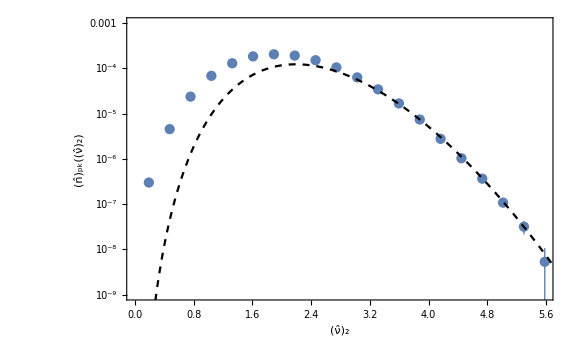

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]]},PlotRange->{10^-9,10^-3}],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black}]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)},{i,CnBins}];
```

```mathematica
nu2inCm[Cm_]=(Sqrt[1-3/2 Cm]-1)/(c Sqrt[As])/.{c->-1.06};
```

```mathematica
nCpt[Cm_]=nnu2PT[nu2inCm[Cm]]nu2inCm'[Cm];
```

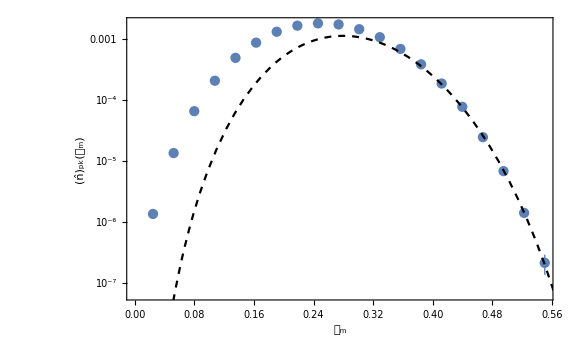

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{Subscript[𝒞, "m"],Subscript[OverHat[n], pk][Subscript[𝒞, "m"]]}],
LogPlot[nCpt[Cm],{Cm,0,0.6},PlotStyle->{Black,Dashed}]]
```

## Lognormal σ^2=0.01

```mathematica
npeak=32;
NL=512;
As=10^-2;(*3.625 10^-3;*)
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
s2=10^-2;
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)kpeak^(2n)]/.{n->4};
```

### peak theory

```mathematica
calPz[lnk_]=1/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
R3=Sqrt[3] σ3/σ4
```

(8 √3)/(ⅇ^(7/100) π)

```mathematica
γn=E^(-2s2)
```

1/ⅇ^(1/50)

```mathematica
ψ1[x_]:=kpeak^2/σ1^2 NIntegrate[E^(2lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2[x_]:=kpeak^4/σ2^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5lnk)calPz[lnk]Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ1pp[x_]:=kpeak^2/σ1^2 NIntegrate[E^(4lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2pp[x_]:=kpeak^4/σ2^2 NIntegrate[E^(6lnk)calPz[lnk]Sinc''[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψ1[x]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψ1p[x]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψ1pp[x]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψ2[x]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψ2pp[x]},{x,10^-2,10,10^-2}];]
```

{8.0738,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=(1/(1-γn^2)(ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1int[x]-1/3 R3^2 σ2^2/σ1^2 ψ2int[x]));
ζp[x_,k3t_]=(1/(1-γn^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
ζpp[x_,k3t_]=(1/(1-γn^2)(ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x])-k3t^2/(γn(1-γn^2))(γn^2 ψ1ppint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2ppint[x]));
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3;
```

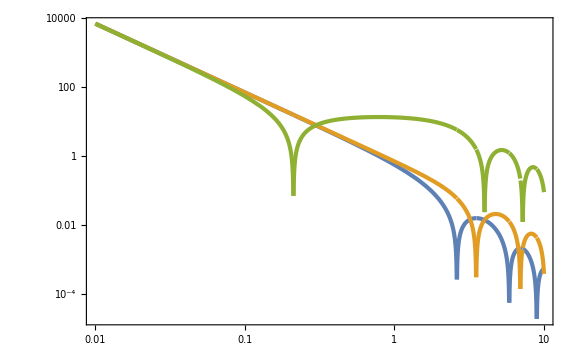

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{10^lnk3t,x/.FindRoot[CmCond[x,10^lnk3t]==0,{x,Min[1/(2 10^lnk3t),1]},WorkingPrecision->30]//Quiet},{lnk3t,-2,2,10^-2}];
```

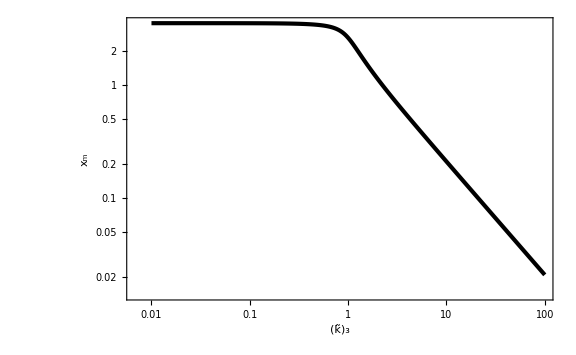

```mathematica
ListLogLogPlot[xmList,PlotRange->Full,FrameLabel->{Subscript[OverTilde[k], 3],Subscript[x, "m"]},PlotStyle->{Black,AbsoluteThickness[3]}]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
nu2inCk[Cm_,k3t_]=(Sqrt[1-3/2 Cm]-1)/(xmint[k3t] σ1^2/σ2 Sqrt[As]ζp[xmint[k3t],k3t]);
dnu2dCm[Cm_,k3t_]=D[nu2inCk[Cm,k3t], Cm]//Simplify;
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)(σ4/σ3)^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
```

```mathematica
nCpt[Cm_]:=NIntegrate[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]],{k3t,5/10,3/2}(*,WorkingPrecision->30,MaxRecursion->12*)]
```

```mathematica
nCpt[6/10]
```

5.94604×10^-10

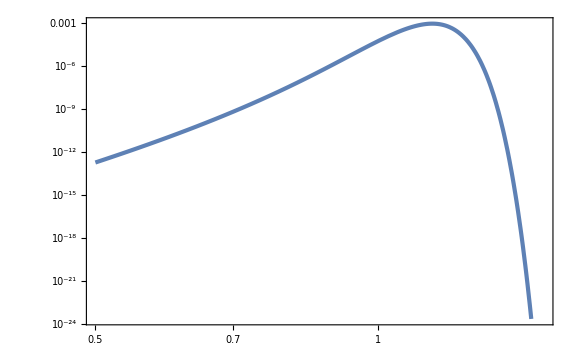

```mathematica
LogLogPlot[npkPT[nu2inCk[Cm,k3t],k3t]Abs[dnu2dCm[Cm,k3t]]/.{Cm->1/10},{k3t,5/10,3/2},WorkingPrecision->30]
```

```mathematica
nCptList=ParallelTable[{Cm,nCpt[Cm]},{Cm,10^-1,6/10,10^-2}];//AbsoluteTiming
```

{130.769,Null}

```mathematica
nCptint[Cm_]=Interpolation[nCptList][Cm];
```

### direct sampling

```mathematica
Nsim=1;
```

```mathematica
Lpeakdata=Table[Import["data/LN_Lpeak_0,01_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighLdata=Table[Select[Lpeakdata[[i]],#[[4]]>4σ2&],{i,Nsim}];
```

```mathematica
Cpeakdata=Table[Import["data/LN_Cpeak_0,01_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"],{i,0,Nsim-1}];
```

```mathematica
HighCdata=Table[Select[Cpeakdata[[i]],#[[5]]>0.45&],{i,Nsim}];
```

```mathematica
matchQ[a_,b_]:=Max[Abs[a[[{1,2,3}]]-b[[{2,3,4}]]]]<=1;
```

```mathematica
onlyInC=Table[Select[HighCdata[[i]],Function[b,!AnyTrue[HighLdata[[i]],matchQ[#,b]&]]],{i,Nsim}]
```

{{{6,8,67,326,0.458735},{6,111,53,218,0.457961},{6,198,498,277,0.453059},{6,199,498,278,0.463101},{6,208,511,334,0.452259},{6,212,329,201,0.459253},{6,217,304,266,0.450274},{6,219,198,371,0.45459},{6,288,70,105,0.454397},{6,298,374,121,0.454417},{6,433,353,299,0.458967},{6,495,137,186,0.455303}}}

```mathematica
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nudata=Flatten[Lpeakdata[[All,All,4]]/σ2];
nunBins=20;
nubinSpec={Min[nudata],Max[nudata],(Max[nudata]-Min[nudata])/nunBins};
```

```mathematica
nubinEdges=HistogramList[nudata,nubinSpec][[1]];
nubinCenters=MovingAverage[nubinEdges,2];
```

```mathematica
nuPDFPerList=HistogramList[(#[[All,4]])/σ2,nubinSpec,"PDF"][[2]]&/@Lpeakdata;
```

```mathematica
numeanPDF=Mean[nuPDFPerList];
(*nusePDF=StandardDeviation[nuPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nnu2Lat=Table[{nubinCenters[[i]],(numeanPDF[[i]]Length[nudata])/(Nsim NL^3)(*±(nusePDF[[i]]Length[nudata])/(Nsim NL^3)*)},{i,nunBins}];
```

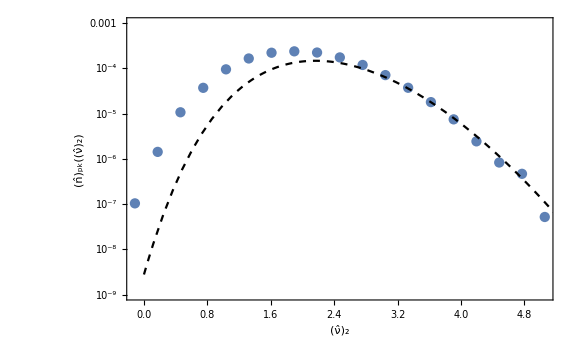

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]]},PlotRange->{10^-9,10^-3}],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black}]]
```

```mathematica
Cdata=Flatten[Cpeakdata[[All,All,5]]];
CnBins=20;
CbinSpec={Min[Cdata],Max[Cdata],(Max[Cdata]-Min[Cdata])/CnBins};
```

```mathematica
CbinEdges=HistogramList[Cdata,CbinSpec][[1]];
CbinCenters=MovingAverage[CbinEdges,2];
```

```mathematica
CPDFPerList=HistogramList[#[[All,5]],CbinSpec,"PDF"][[2]]&/@Cpeakdata;
```

```mathematica
CmeanPDF=Mean[CPDFPerList];
(*CsePDF=StandardDeviation[CPDFPerList]/Sqrt[Nsim];*)
```

```mathematica
nCLat=Table[{CbinCenters[[i]],(CmeanPDF[[i]]Length[Cdata])/(Nsim NL^3)(*±(CsePDF[[i]]Length[Cdata])/(Nsim NL^3)*)},{i,CnBins}];
```

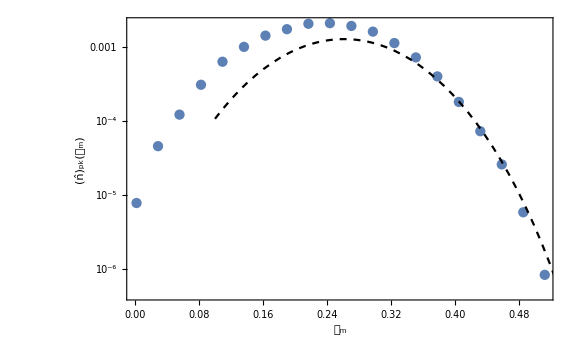

```mathematica
Show[ListLogPlot[nCLat,Joined->False,FrameLabel->{Subscript[𝒞, "m"],Subscript[OverHat[n], pk][Subscript[𝒞, "m"]]}],
LogPlot[nCptint[Cm],{Cm,1/10,6/10},PlotStyle->{Black,Dashed}]]
```